## V(ϕ) demonstration

```mathematica
basisBosonD20=Import[NotebookDirectory[]<>"basisBosonD20.WXF"]//BinaryDeserialize;
phiNMatricesD20=(Import[NotebookDirectory[]<>"phiNMatsEvenD20.WXF"]//BinaryDeserialize);
dictionary=MapIndexed[#1->#2[[1]]&,Flatten[MapIndexed[
Table[#2-{1,0},Length[#1]]&,
basisBosonD20[[1]],
{2}
],2]]//Association;
idxLowerDmax[dmax_]:=KeySelect[dictionary,#[[1]]+#[[2]]<=dmax&]//Values;
cos[β_,phiNMats_]:=KeyValueMap[If[#1==2,1,(ⅈ β)^(#1-2)]*#2&,phiNMats]//Total;
```

```mathematica
cosMatFromCorrD20Δ[Δ_]:=8π Δ cos[√(4π Δ),phiNMatricesD20];
```

```mathematica
LCTEvals20[Δ_?NumericQ]:=LCTEvals20[Δ]=cosMatFromCorrD20Δ[Δ]//Eigenvalues[#,-30]&//SortBy[Abs]
LCTMgap20n[Δ_?NumericQ,n_]:=LCTEvals20[Δ][[n]]
LCTMgap20[Δ_?NumericQ]:=LCTMgap20n[Δ,1]
```

```mathematica
breathermass[n_,Δ_]:=2 Sin[(π n (4π Δ)/(8π-4π Δ))/2];
Msoliton[Δ_,μ_]=2 Gamma[ξ/2]/(√π Gamma[1/2+ξ/2])(μ π Gamma[1-bsq]/Gamma[bsq])^(1/(2-2bsq))/.ξ->bsq/(1-bsq)/.bsq->Δ/2//Simplify;
vev[Δ_,μ_]=Assuming[Δ>0,-1/((1+bsq) Gamma[-bsq])π^(1+1/2 (2+2 bsq)) Csc[(bsq π)/(1+bsq)] Gamma[1+bsq] ((π^(1/2+1/(2+2 bsq)) (-(μ Gamma[1+bsq])/Gamma[-bsq])^(1/(2+2 bsq)))/(Gamma[1/(2+2 bsq)] Gamma[1+bsq/(2+2 bsq)]))^(-2 bsq) (Gamma[1/(2+2 bsq)] Gamma[1+bsq/(2+2 bsq)])^(-2-2 bsq)/.bsq->-Δ/2//FullSimplify]/.μ->-μ;
```

```mathematica
LCTSpec20Tab=Monitor[Table[{Δ,LCTEvals20[Δ]},{Δ,0,4/3,0.01}],Δ]
LCTSpec20NegTab=Monitor[Table[{Δ,LCTEvals20[Δ]},{Δ,-5.001,0.1,0.025}],Δ]
```

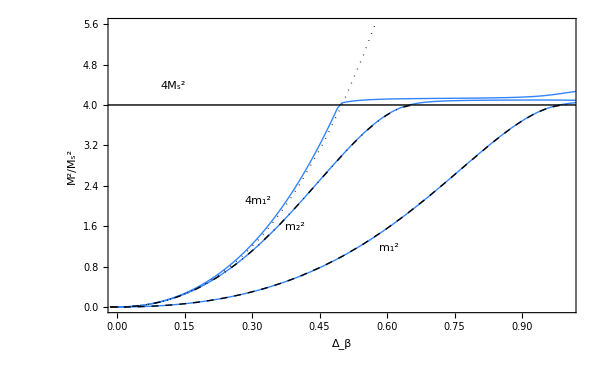

```mathematica
p20LC=ListPlot[{{#[[1]],(#[[2,1]])/(4π)π Tan[(π Δ)/(4-2Δ)]/(2-Δ)/.Δ->#[[1]]}&/@Take[Drop[LCTSpec20Tab,{101}],115],{#[[1]],(#[[2,2]])/(4π)π Tan[(π Δ)/(4-2Δ)]/(2-Δ)/.Δ->#[[1]]}&/@Take[Drop[LCTSpec20Tab,{101}],115],{#[[1]],(#[[2,3]])/(4π)π Tan[(π Δ)/(4-2Δ)]/(2-Δ)/.Δ->#[[1]]}&/@Take[Drop[LCTSpec20Tab,{101}],115]},Joined->True,PlotRange->{{0,1},{0,5.6}},PlotStyle->{(*{Thick,Red},{Thick,Purple},{Thick,Blue},*){Thick,Lighter[Hue[0.6],0.2]}},Frame->True,FrameLabel->{"Δ_β","M^2/M_s^2"},ImageSize->600,BaseStyle->{FontFamily->"Times",FontSize->24},Epilog->{Text["m_1^2",Scaled[{0.6,.22}]],Text["m_2^2",Scaled[{0.4,.29}]],Text["4m_1^2",Scaled[{0.32,.38}]],Text["4M_s^2",Scaled[{0.14,.77}]]}];
pSG=Plot[{If[Δ<1,breathermass[1,Δ]^2],If[Δ<2/3,(breathermass[2,Δ])^2],If[Δ<1,4(breathermass[1,Δ])^2],4},{Δ,-1,1.3},PlotRange->{{-1,2},{-1,5.6}},PlotStyle->{{Thick,Black,Dashed},{Thick,Black,DotDashed},{Thick,Black,Dotted},{Thick,Black}}];
Show[p20LC,pSG]
```

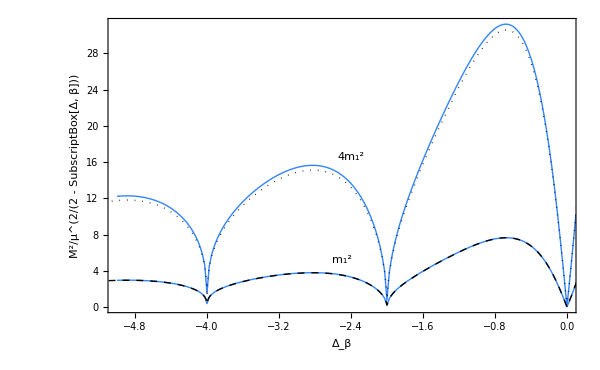

```mathematica
p20LCNegB=ListPlot[{{#[[1]],(#[[2,1]])/(4π)π Tan[(π Δ)/(4-2Δ)]/(2-Δ)Abs[Msoliton[Δ,1]^2]/.Δ->#[[1]]}&/@LCTSpec20NegTab,{#[[1]],(#[[2,2]])/(4π)π Tan[(π Δ)/(4-2Δ)]/(2-Δ)Abs[Msoliton[Δ,1]^2]/.Δ->#[[1]]}&/@LCTSpec20NegTab},Joined->True,PlotRange->{{Automatic,0},Automatic},PlotStyle->{{Thick,Lighter[Hue[0.6],0.2]}},Frame->True,FrameLabel->{"Δ_β","M^2/μ^(2/(2 - SubscriptBox[Δ, β]))"},ImageSize->600,BaseStyle->{FontFamily->"Times",FontSize->24},Epilog->{Text["m_1^2",Scaled[{0.5,.18}]],Text["4m_1^2",Scaled[{0.52,.53}]]}];
pSGB=Plot[{If[Δ<1,breathermass[1,Δ]^2 Abs[Msoliton[Δ,1]^2]],If[Δ<1,4(breathermass[1,Δ])^2 Abs[Msoliton[Δ,1]^2]]},{Δ,-9,1.3},PlotRange->{{-8,9},Automatic},PlotStyle->{{Thick,Black,Dashed},{Thick,Black,Dotted}}];
Show[p20LCNegB,pSGB]
```

```mathematica
(*Equation 4.36 of 9211053, Fmin=FFminProdPart*FminIntPart. γ here is related to the B in 9211053 by γ=B/(π/2).*)
```

```mathematica
ClearAll[FFminProdPart]
FFminProdPart[γ_][N_][θ_]:=Product[(((1+(((I Pi-θ)/(2Pi))/(k+1/2))^2)(1+(((I Pi-θ)/(2Pi))/(k+3/2-γ/(2Pi)))^2)(1+(((I Pi-θ)/(2Pi))/(k+1+γ/(2Pi)))^2))/((1+(((I Pi-θ)/(2Pi))/(k+3/2))^2)(1+(((I Pi-θ)/(2Pi))/(k+1/2+γ/(2Pi)))^2)(1+(((I Pi-θ)/(2Pi))/(k+1-γ/(2Pi)))^2)))^(k+1),{k,0,N-1}];

ClearAll[FminIntPart] 
(*this is not really needed*)
FminIntPart[γ_][NN_][θ_?NumberQ]:=FminIntPart[γ][NN][θ]=Module[{int,x,cut=1000},
int=8/x(Sinh[(x γ)/(2π)]Sinh[x/2(1-γ/π)]Sinh[x/2])/Sinh[x]^2(NN+1-NN Exp[-2x])Exp[-2NN x] Sin[(x (I π-θ))/(2π)]^2;
int=NIntegrate[int,{x,0,cut},Method->{"GlobalAdaptive","MaxErrorIncreases"->10000,Method->"GaussKronrodRule"},MaxRecursion->100,WorkingPrecision->200](*;
Exp[int]//N*)
]
```

```mathematica
dataCMomentFFShGDeltaHalf=Monitor[With[
{myγ=(2/5*Pi/2)},
Table[
3/8 NIntegrate[(2Cosh[β])^-n Abs[F[2β]]^2/Cosh[β]^4/.F->Function[θ,-2FFminProdPart[myγ][10][θ]],{β,0,30},WorkingPrecision->30],
{n,2,40,2}
]
],n]
```

{0.174838820332863095229272046784,0.0337414271616643406346062918451,0.00684568900471612547149465796691,0.00143496625954699497664932525046,0.000307837716232809170417985450962,0.0000671968976606105090732448663648,0.0000148687018420954716404168976777,3.32617088929652154769705812221×10^-6,7.50809357115661352303470838535×10^-7,1.70766324697240978779268461509×10^-7,3.90912203337986319706390605288×10^-8,8.9986984005852207609762805519×10^-9,2.08160079748603621517376269685×10^-9,4.83595689819966375893336869239×10^-10,1.12778827977510140585395937997×10^-10,2.63912161596437411562072927697×10^-11,6.19485228146516967355366067667×10^-12,1.45819836830943172316311092221×10^-12,3.44118538517964435378552771934×10^-13,8.13975406411099758180895793789×10^-14}

```mathematica
ClearAll[proj,cosh,numStates,dictionary]
(*Number of states at a given particle sector and degree *)
numStates[n_,bDeg_]:=numStates[n,bDeg]=With[
	{Δ=n+bDeg},
	Coefficient[Normal@Series[x^n Product[1/(1-x^k),{k,2,n}],{x,0,Δ}],x^Δ]
];
dictionary[Δmax_]:=dictionary[Δmax]=MapIndexed[#2[[1]]->#1&,Table[
{n,n+bDeg},
{n,1,Δmax},{bDeg,0,Δmax-n},{i,numStates[n,bDeg]}
]//Flatten[#,2]&]//Association
proj[ΔmaxLow_,Δmax_]:=proj[ΔmaxLow,Δmax]=Select[dictionary[Δmax],#[[2]]<=ΔmaxLow&]//Keys;
cosh[g_,phiNMats_]:=KeyValueMap[If[#1==2,1,(g)^(#1-2)]*#2&,phiNMats]//Total
```

```mathematica
esysDeltaHalf=Monitor[Table[Module[
{evals,evecs,bb=2/5,g},
g=(2 √bb √(2 π))/(√(2-bb));
{evals,evecs}=SortBy[Eigensystem[cosh[g,phiNMatricesD20][[
proj[ΔmaxLow,20],proj[ΔmaxLow,20]
]]]//Transpose,First]//Transpose;
<|
"B"->bb,
"g"->g,
"ΔmaxLow"->ΔmaxLow,
"evals"->evals,
"evecs"->evecs
|>
],{ΔmaxLow,6,20,2}],ΔmaxLow];
```

```mathematica
esysDelta8=Monitor[Table[Module[
{evals,evecs,bb=2-2/5,g},
g=(2 √bb √(2 π))/(√(2-bb));
{evals,evecs}=SortBy[Eigensystem[cosh[g,phiNMatricesD20][[
proj[ΔmaxLow,20],proj[ΔmaxLow,20]
]]]//Transpose,First]//Transpose;
<|
"B"->bb,
"g"->g,
"ΔmaxLow"->ΔmaxLow,
"evals"->evals,
"evecs"->evecs
|>
],{ΔmaxLow,6,20,2}],ΔmaxLow];
```

```mathematica
extrapolateMoment[esysArray_,powDiv2_]:=Module[
{data},
data={1/(#ΔmaxLow)^2,Total[((#evals)/(#evals[[1]]))^-powDiv2*(#evecs[[;;,2]])^2]}&/@esysArray;
Fit[data[[-4;;]],{1,x},x]/.x->0
]
```

```mathematica
Table[
{n,extrapolateMoment[esysDeltaHalf,n/2],extrapolateMoment[esysDelta8,n/2]},
{n,2,40,2}
]//Transpose//Append[#,dataCMomentFFShGDeltaHalf//N]&//Transpose//TableForm[#,TableHeadings->{None, {"n","Δ=1/2","Δ=8","integrability"}}]&
```

n | Δ=1/2 | Δ=8 | integrability
2 | 0.175051 | 0.175614 | 0.174839
4 | 0.033748 | 0.0338842 | 0.0337414
6 | 0.0068463 | 0.00687572 | 0.00684569
8 | 0.00143513 | 0.00144139 | 0.00143497
10 | 0.000307892 | 0.000309196 | 0.000307838
12 | 0.0000672135 | 0.000067477 | 0.0000671969
14 | 0.0000148736 | 0.0000149241 | 0.0000148687
16 | 3.32759×10^-6 | 3.33642×10^-6 | 3.32617×10^-6
18 | 7.51213×10^-7 | 7.52471×10^-7 | 7.50809×10^-7
20 | 1.70879×10^-7 | 1.70955×10^-7 | 1.70766×10^-7
22 | 3.91223×10^-8 | 3.90808×10^-8 | 3.90912×10^-8
24 | 9.00715×10^-9 | 8.98157×10^-9 | 8.9987×10^-9
26 | 2.08388×10^-9 | 2.07367×10^-9 | 2.0816×10^-9
28 | 4.84203×10^-10 | 4.80702×10^-10 | 4.83596×10^-10
30 | 1.1294×10^-10 | 1.1183×10^-10 | 1.12779×10^-10
32 | 2.64338×10^-11 | 2.60988×10^-11 | 2.63912×10^-11
34 | 6.20611×10^-12 | 6.10831×10^-12 | 6.19485×10^-12
36 | 1.46118×10^-12 | 1.43332×10^-12 | 1.4582×10^-12
38 | 3.4491×10^-13 | 3.37118×10^-13 | 3.44119×10^-13
40 | 8.16096×10^-14 | 7.94609×10^-14 | 8.13975×10^-14

## Schwinger Model

```mathematica
spectrumSchwinger=Module[{δb=0.0001,evals},Table[
Thread[{e,
evals=(√Eigenvalues[4/δb cos[√(4π)-δb,phiNMatricesD20]+e^2*phiNMatricesD20[2]]-2)//TakeSmallest[40];
(evals[[;;]]-evals[[1]])/(evals[[2]]-evals[[1]])
}],
{e,Subdivide[0,1,100][[2;;]]}
]//Transpose];
```

```mathematica
airyPrimeZeros={1.0187929716474702,3.2481975821798366,4.820099211178736,6.163307355639487,7.372177255047771,8.488486734019725,9.535449052433549,10.527660396957407,11.475056633480245,12.384788371845746,13.26221896166521,14.111501970462998,14.935937196720518,15.738201373692538,16.520503825433792,17.28469505021644,18.032344622504393,18.764798437665956,19.483221656567235,20.188631509463374};
```

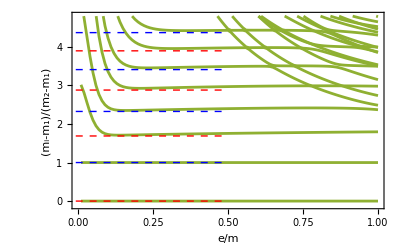
-Graphics- | Δ_max==20

```mathematica
pltSchwinger=Grid[{{Show[
ListPlot[
spectrumSchwinger,
PlotStyle->ColorData[97][3],
Joined->True,
PlotRange->{{0,1},{0,4.8}}
],
Plot[
(*(airyPrimeZeros[[3;;7]]-airyPrimeZeros[[1]])/(airyPrimeZeros[[2]]-airyPrimeZeros[[1]])//Evaluate*)
(airyPrimeZeros[[;;4]]-airyPrimeZeros[[1]])/(-AiryAiZero[1]-airyPrimeZeros[[1]])//Evaluate,
{x,-0.1,.5},
PlotStyle->Directive[Red,Dashed,Thick]
],
Plot[
(*(-AiryAiZero[Range[5]]-airyPrimeZeros[[1]])/(airyPrimeZeros[[2]]-airyPrimeZeros[[1]])//Evaluate*)
(-AiryAiZero[Range[4]]-airyPrimeZeros[[1]])/(-AiryAiZero[1]-airyPrimeZeros[[1]])//Evaluate,
{x,-0.1,.5},
PlotStyle->Directive[Blue,Dashed,Thick]
],
PlotRange->{{0,1},{-0.1,4.8}},
Frame->True,
FrameLabel->{
Row[{e,"/",m}],(Subscript[m, i]-Subscript[m, 1])/(Subscript[m, 2]-Subscript[m, 1])
},
BaseStyle->{Black,FontFamily->"Linux Libertine",FontSize->12},
ImageSize->400
],
Grid[{
{Subscript[Δ, max]==20},
{
LineLegend[
{ColorData[97][3],Directive[Red,Dashed],Directive[Blue,Dashed]},
{"LCT",(Subscript[λ, n]^("+")-Subscript[λ, 1]^("+"))/(Subscript[λ, 1]^("1")-Subscript[λ, 1]^("+")),
(Subscript[λ, n]^("-")-Subscript[λ, 1]^("+"))/(Subscript[λ, 1]^("1")-Subscript[λ, 1]^("+"))
}
]}}]
}}
]
```

```mathematica
spectrumSchwingerLargeE=Module[{δb=0.0001,evals},Table[
Thread[{m,
evals=Eigenvalues[(4 m^2)/δb cos[√(4π)-δb,phiNMatricesD20]+phiNMatricesD20[2]]//TakeSmallest[40];
evals[[;;]]/evals[[1]]
}],
{m,Subdivide[0,3,100][[2;;]]}
]//Transpose];
```

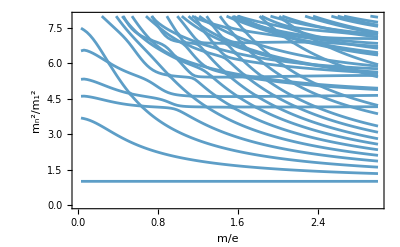

```mathematica
pltSchwingerLargeE=ListPlot[spectrumSchwingerLargeE,
PlotRange->{0,8},
Joined->True,
PlotStyle->ColorData[97][7],
Frame->True,
FrameLabel->{
Row[{m,"/",e}],Row[{Subscript[m, n]^2,"/",Subscript[m, 1]^2}]
},
LabelStyle->{Black,FontFamily->"Linux Libertine",FontSize->12},
ImageSize->400
]
```